## Input

### Derivatives of Shape Function

```mathematica
hhp=({{-1.5, -0.5, 0.5}, {2, 0, -2}, {-0.5, 0.5, 1.5}});
(*hhp=Transpose[hhp];*)
```

### Weight Function

```mathematica
wj=({{1.0/3}, {4.0/3}, {1.0/3}});
```

### Beam Length and Cross-Section Constants

```mathematica
L=1;
EA=10^4;
GA=10^4;
EI=10^2;
(*EA=70*10^9;
GA=5.*27*10^9/6.;
EI=70*10^9/12.;*)
Stif0=Table[0,{i,6},{j,6}];
Stif0[[1,1]]=3.50000*10^8;
Stif0[[2,2]]=1.09162*10^8;
Stif0[[3,3]]=1.09162*10^8;
Stif0[[4,4]]=7.57037*10^4;
Stif0[[5,5]]=7.28000*10^4;
Stif0[[6,6]]=2.91900*10^5;
m00=1.35*10^1;
mEta0=({{0}, {0}, {0}});
rho0=({{1.40625*10^-2, 0, 0}, {0, 2.81250*10^-3, 0}, {0, 0, 1.12500*10^-2}});
```

### Jacobian and Initial Value

```mathematica
Jaco=L/2;
uuNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
uuN0={{0.},{0},{0},{0},{0},{0},{0.5},{0},{0},{0},{0},{0},{1.0},{0},{0},{0},{0},{0}};
uuNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
vvNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
aaNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
xxNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
vvNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
aaNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
xxNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
tolx=1.0*10^-6;
```

### Sin Force Function

```mathematica
Af=1.0*10^5;
ωf=20;
Fext[t_]:=Af*Sin[ωf*t];
```

## Utilities

```mathematica
Tilde[v1_,v2_,v3_]:=Module[{m12,m13,m21,m23,m31,m32},
m12=-v3;m13=v2;
m21=v3;m23=-v1;
m31=-v2;m32=v1;
{{0,m12,m13},{m21,0,m23},{m31,m32,0}}]
```

## CRV Functions

### CRV Compose 0

```mathematica
CrvCompose0[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=cc1,pp2=cc2,pp3=cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Compose 1

```mathematica
CrvCompose1[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=-cc1,pp2=-cc2,pp3=-cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Matrix R

```mathematica
CrvMatrixR[cc1_,cc2_,cc3_]:=Module[{c0,c1=cc1/4,c2=cc2/4,c3=cc3/4,tr0,R0,R1,R2,R3,R4,R5,R6,R7,R8},
c0=0.5*(1-c1*c1-c2*c2-c3*c3);
tr0=1-c0;
tr0=2/(tr0*tr0);
R0=tr0*(c1*c1+c0*c0)-1;
R1=tr0*(c1*c2+c0*c3);
R2=tr0*(c1*c3-c0*c2);
R3=tr0*(c1*c2-c0*c3);
R4=tr0*(c2*c2+c0*c0)-1;
R5=tr0*(c2*c3+c0*c1);
R6=tr0*(c1*c3+c0*c2);
R7=tr0*(c2*c3-c0*c1);
R8=tr0*(c3*c3+c0*c0)-1;
{{R0,R3,R6},{R1,R4,R7},{R2,R5,R8}}];
```

### CRV Matrix H

```mathematica
CrvMatrixH[cc1_,cc2_,cc3_]:=Module[{cf1=cc1/4,cf2=cc2/4,cf3=cc3/4,cq,ocq,aa,cb0,cb1,cb2,cb3,H0,H1,H2,H3,H4,H5,H6,H7,H8},
cq=cf1*cf1+cf2*cf2+cf3*cf3;
ocq=1+cq;
aa=2*ocq*ocq;
cb0=2*(1-cq)/aa;
cb1=cc1/aa;
cb2=cc2/aa;
cb3=cc3/aa;
H0=cb1*cf1+cb0;
H1=cb2*cf1+cb3;
H2=cb3*cf1-cb2;
H3=cb1*cf2-cb3;
H4=cb2*cf2+cb0;
H5=cb3*cf2+cb1;
H6=cb1*cf3+cb2;
H7=cb2*cf3-cb1;
H8=cb3*cf3+cb0;
{{H0,H3,H6},{H1,H4,H7},{H2,H5,H8}}];
```

## GLL Shape Function

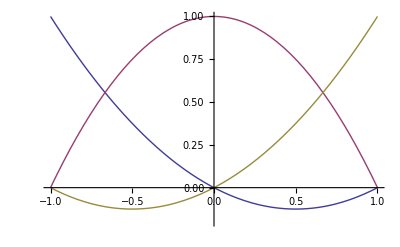

```mathematica
norder=2;
GLL1=-1.0;
GLL2=0.0;
GLL3=1.0;
GL1=-Sqrt[3]/3.0;
GL2=Sqrt[3]/3.0;
hh1[s_]:=Piecewise[{{1,s==GLL1},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL1]*(s-GLL1)),GLL1<s≤1}}];
hh2[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),-1≤s<GLL2},{1,s==GLL2},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),GLL2<s≤1}}];
hh3[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL3]*(s-GLL3)),-1≤s<GLL3},{1,s==GLL3}}];
Plot[{hh1[s],hh2[s],hh3[s]},{s,-1,1},PlotRange->{{-1,1},{-0.2,1}}]
```

## Time Scheme Parameters and Coefficients

```mathematica
rhoinf=1.0;
```

```mathematica
tr0=rhoinf+1.0;
alfam=(2.0*rhoinf-1.0)/tr0;
alfaf=rhoinf/tr0;
gama=0.5-alfam+alfaf;
beta=0.25*(1.0-alfam+alfaf)^2;
```

```mathematica
deltat=0.001;
deltat2=deltat^2;
```

```mathematica
oalfaM=1.0-alfam;
tr0=alfaf/oalfaM;
tr1=alfam/oalfaM;
tr2=(1.0-alfaf)/oalfaM;
coef={{0},{0},{0},{0},{0},{0},{0},{0},{0}};
coef[[1,1]]=beta*tr0*deltat2;
coef[[2,1]]=(0.5-beta/oalfaM)*deltat2;
coef[[3,1]]=gama*tr0*deltat;
coef[[4,1]]=(1.0-gama/oalfaM)*deltat;
coef[[5,1]]=tr0;
coef[[6,1]]=-tr1;
coef[[7,1]]=gama*tr2*deltat;
coef[[8,1]]=beta*tr2*deltat2;
coef[[9,1]]=tr2;
coef
```

{{2.5×10^-7},{0.},{0.0005},{0.},{1.},{-1.},{0.0005},{2.5×10^-7},{1.}}

## First Iteration

### (*Predictor Step*)

```mathematica
vvNf=vvNi+coef[[3,1]]*aaNi+coef[[4,1]]*xxNi;
aaNf=Table[0,{i,18},{j,1}];
xxNf=coef[[5,1]]*aaNi+coef[[6,1]]*xxNi;
tr=Table[0,{i,1,18},{j,1}];
tr=deltat*vvNi+coef[[1,1]]*aaNi+coef[[2,1]]*xxNi;
tempN1=CrvCompose0[tr[[4,1]],tr[[5,1]],tr[[6,1]],uuNi[[4,1]],uuNi[[5,1]],uuNi[[6,1]]];
tempN2=CrvCompose0[tr[[10,1]],tr[[11,1]],tr[[12,1]],uuNi[[10,1]],uuNi[[11,1]],uuNi[[12,1]]];
tempN3=CrvCompose0[tr[[16,1]],tr[[17,1]],tr[[18,1]],uuNi[[16,1]],uuNi[[17,1]],uuNi[[18,1]]];
Do[uuNf[[i,1]]=uuNi[[i,1]]+tr[[i,1]],{i,3}]
Do[uuNf[[i+3,1]]=tempN1[[i,1]],{i,3}];
Do[uuNf[[i+6,1]]=tr[[i+6,1]],{i,3}];
Do[uuNf[[i+3+6,1]]=tempN2[[i,1]],{i,3}];
Do[uuNf[[i+12,1]]=tr[[i+12,1]],{i,3}];
Do[uuNf[[i+3+12,1]]=tempN3[[i,1]],{i,3}];
uuNf
vvNf
aaNf
xxNf
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

### (*END Predictor Step*)

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm
E10N2//MatrixForm
E10N3//MatrixForm
```

(1.
0.
0.)

(1.
0.
0.)

(1.
0.
0.)

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
0.)

(1.
0.
0.)

(1.
0.
0.)

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]];
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]];
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]];
```

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]]; 
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]]; 
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]];
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm;
rrpN2 // MatrixForm;
rrpN3 // MatrixForm;
```

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
0.
0.)

(0.
0.
0.)

(0.
0.
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(0.
0.
0.
0.
0.
0.)

(0.
0.
0.
0.
0.
0.)

(0.
0.
0.
0.
0.
0.)

(0
0
0
0.
0.
0.)

(0
0
0
0.
0.
0.)

(0
0
0
0.
0.
0.)

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | 0. | 0. | 1.09162×10^8)

```mathematica
C22N3//MatrixForm
```

(75703.7 | 0. | 0.
0. | 72800. | 0.
0. | 0. | 291900.)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
```

```mathematica
FiN2//MatrixForm
```

(0.
0.
0.
0.
0.
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
```

```mathematica
MiN2//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
```

```mathematica
KiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
```

```mathematica
GiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0. | 0. | -1.81937×10^7
0. | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0. | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 25234.6 | 0. | 0.
0. | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 1.81937×10^7 | 0. | 0. | 0. | 97300.
-9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.86667×10^9 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7
0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 403753. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0.
0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 0. | 0. | 0. | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400.
1.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 8.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0. | 0. | -5.4581×10^7
0. | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0. | 0. | 25234.6 | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 176642. | 0. | 0.
0. | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | 0. | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | -5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (Compute Elemental Matrices: elg,elm,add Ki into elk, add Fi into elf*)

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*KiN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*KiN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*KiN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0. | 0. | -1.81937×10^7
0. | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0. | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 25234.6 | 0. | 0.
0. | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 1.81937×10^7 | 0. | 0. | 0. | 97300.
-9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.86667×10^9 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7
0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 403753. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0.
0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 0. | 0. | 0. | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400.
1.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 8.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0. | 0. | -5.4581×10^7
0. | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0. | 0. | 25234.6 | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 176642. | 0. | 0.
0. | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | 0. | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | -5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7)

```mathematica
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FiN1;
Do[elf[[i,1]]=elf[[i,1]]-temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FiN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]-temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FiN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]-temp61[[i,1]],{i,6}];
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
elm=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*MiN1;
Do[elm[[i,j]]=elm[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*MiN2;
Do[elm[[i+6,j+6]]=elm[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*MiN3;
Do[elm[[i+12,j+12]]=elm[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elm//MatrixForm
```

(2.25 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 2.25 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 2.25 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0.00234375 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0.00046875 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0.001875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 9. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 9. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.009375 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.001875 | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.0075 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.25 | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 2.25 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 2.25 | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.00234375 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.00046875 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.001875)

```mathematica
elg=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*GiN1;
Do[elg[[i,j]]=elg[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*GiN2;
Do[elg[[i+6,j+6]]=elg[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*GiN3;
Do[elg[[i+12,j+12]]=elg[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elg//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.)

### (END Compute Elemental Matrices: elg,elm,add Ki into elk, add Fi into elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(206.417 | 0. | 0. | 0. | 0. | 0. | -233.333 | 0. | 0. | 0. | 0. | 0. | 29.1667 | 0. | 0. | 0. | 0. | 0.
0. | 65.9278 | 0. | 0. | 0. | 13.6452 | 0. | -72.7747 | 0. | 0. | 0. | 18.1937 | 0. | 9.09683 | 0. | 0. | 0. | -4.54842
0. | 0. | 65.9278 | 0. | -13.6452 | 0. | 0. | 0. | -72.7747 | 0. | -18.1937 | 0. | 0. | 0. | 9.09683 | 0. | 4.54842 | 0.
0. | 0. | 0. | 0.0465042 | 0. | 0. | 0. | 0. | 0. | -0.0504691 | 0. | 0. | 0. | 0. | 0. | 0.00630864 | 0. | 0.
0. | 0. | -13.6452 | 0. | 4.59135 | 0. | 0. | 0. | 18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | -4.54842 | 0. | 0.00606667 | 0.
0. | 13.6452 | 0. | 0. | 0. | 4.72057 | 0. | -18.1937 | 0. | 0. | 0. | -0.1946 | 0. | 4.54842 | 0. | 0. | 0. | 0.024325
-233.333 | 0. | 0. | 0. | 0. | 0. | 475.667 | 0. | 0. | 0. | 0. | 0. | -233.333 | 0. | 0. | 0. | 0. | 0.
0. | -72.7747 | 0. | 0. | 0. | -18.1937 | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | 0. | 0. | 18.1937
0. | 0. | -72.7747 | 0. | 18.1937 | 0. | 0. | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | -18.1937 | 0.
0. | 0. | 0. | -0.0504691 | 0. | 0. | 0. | 0. | 0. | 0.110313 | 0. | 0. | 0. | 0. | 0. | -0.0504691 | 0. | 0.
0. | 0. | -18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | 0. | 0. | 18.2926 | 0. | 0. | 0. | 18.1937 | 0. | -0.0485333 | 0.
0. | 18.1937 | 0. | 0. | 0. | -0.1946 | 0. | 0. | 0. | 0. | 0. | 18.5904 | 0. | -18.1937 | 0. | 0. | 0. | -0.1946
29.1667 | 0. | 0. | 0. | 0. | 0. | -233.333 | 0. | 0. | 0. | 0. | 0. | 206.417 | 0. | 0. | 0. | 0. | 0.
0. | 9.09683 | 0. | 0. | 0. | 4.54842 | 0. | -72.7747 | 0. | 0. | 0. | -18.1937 | 0. | 65.9278 | 0. | 0. | 0. | -13.6452
0. | 0. | 9.09683 | 0. | -4.54842 | 0. | 0. | 0. | -72.7747 | 0. | 18.1937 | 0. | 0. | 0. | 65.9278 | 0. | 13.6452 | 0.
0. | 0. | 0. | 0.00630864 | 0. | 0. | 0. | 0. | 0. | -0.0504691 | 0. | 0. | 0. | 0. | 0. | 0.0465042 | 0. | 0.
0. | 0. | 4.54842 | 0. | 0.00606667 | 0. | 0. | 0. | -18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | 13.6452 | 0. | 4.59135 | 0.
0. | -4.54842 | 0. | 0. | 0. | 0.024325 | 0. | 18.1937 | 0. | 0. | 0. | -0.1946 | 0. | -13.6452 | 0. | 0. | 0. | 4.72057)

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 475.667 | 0. | 0. | 0. | 0. | 0. | -233.333 | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | 0. | 0. | 18.1937
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | -18.1937 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.110313 | 0. | 0. | 0. | 0. | 0. | -0.0504691 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 18.2926 | 0. | 0. | 0. | 18.1937 | 0. | -0.0485333 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 18.5904 | 0. | -18.1937 | 0. | 0. | 0. | -0.1946
0 | 0 | 0 | 0 | 0 | 0 | -233.333 | 0. | 0. | 0. | 0. | 0. | 206.417 | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | -72.7747 | 0. | 0. | 0. | -18.1937 | 0. | 65.9278 | 0. | 0. | 0. | -13.6452
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | -72.7747 | 0. | 18.1937 | 0. | 0. | 0. | 65.9278 | 0. | 13.6452 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | -0.0504691 | 0. | 0. | 0. | 0. | 0. | 0.0465042 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | -18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | 13.6452 | 0. | 4.59135 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 18.1937 | 0. | 0. | 0. | -0.1946 | 0. | -13.6452 | 0. | 0. | 0. | 4.72057)

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

1999.87

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1999.87
0.
0.
0.)

```mathematica
Norm[RHS]
```

1999.87

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
158.363
0.
-705.483
0.
0.
0.
705.381
0.
-1476.28
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.0000395906
0.
-0.000176371
0.
0.
0.
0.000176345
0.
-0.000369071
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
vvNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.0791813
0.
-0.352741
0.
0.
0.
0.352691
0.
-0.738142
0.)

## Second Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-0.0000179827)

(1.
0.
0.000176345)

(1.
0.
0.000370673)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

0.00006415

0.000288541

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-0.000176371},{0.}}

{{0.},{-0.000369071},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-0.0000725506

-0.000285634

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -0.000176371
0. | 1. | 0.
0.000176371 | 0. | 1.)

(1. | 0. | -0.000369071
0. | 1. | 0.
0.000369071 | 0. | 1.)

```mathematica
0.9999999420233912
```

1.

```mathematica
0.9999997583428208
```

1.

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 42476.8 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
42476.8 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -38.1307
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -38.1307 | 0. | 291900.)

(3.5×10^8 | 0. | 88886.4 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
88886.4 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -79.7918
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -79.7918 | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-0.000176371
0.
0.
-0.000369071
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-0.000336411
0.)

(0.
-0.000369071
0.)

(0.
-0.000401731
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-0.000350215

-0.000387927

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-0.000336411
0.)

(0.
-0.000369071
0.)

(0.
-0.000401731
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
StifN2//MatrixForm
eeeN2//MatrixForm
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN2//MatrixForm
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(3.5×10^8 | 0. | 42476.8 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
42476.8 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -38.1307
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -38.1307 | 0. | 291900.)

(1.55533×10^-8
0.
-2.53842×10^-8
0.
-0.000369071
0.)

(5.44258
0.
-2.77033
0.
-26.8684
0.)

(0.
0.
-1963.02
0.
-24.4907
0.)

(5.44258
0.
-2.77033
0.
-26.8684
0.)

(23.9798
0.
174.88
0.
-29.246
0.)

(0
0
0
0.
-1963.02
0.)

(0
0
0
0.
-2.77129
0.)

(0
0
0
0.
174.871
0.)

```mathematica
3.499999720740596*5.79766+82009.91844498752*-2.024604649864892*10^-8
```

20.2901

```mathematica
3.499999720740596*5.79766
```

20.2918

```mathematica
82009.91844498752*-2.024604649864892*10^-8
```

-0.00166038

```mathematica
eeeN2//MatrixForm
```

(1.55533×10^-8
0.
-2.53842×10^-8
0.
-0.000369071
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

-917.029

317.284

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 14.9339 | 0. | -40463.4
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | -40288.5 | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(0.
0.
9522.64
0.
-4.15205
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -0.000699899 | 0. | -7.93668
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 5.95251 | 0. | -0.00174975)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 43132.2 | 0. | -2165.45 | 0. | -9.33333×10^8 | 0. | -59257.6 | 0. | 12831.2 | 0. | 1.16667×10^8 | 0. | 16125.3 | 0. | -6779.06 | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | -12835.3 | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 6714.76 | 0. | -1.81937×10^7
43132.2 | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | -59257.6 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 16125.3 | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 276.206 | 0. | 0. | 0. | -201877. | 0. | 35.2823 | 0. | 0. | 0. | 25234.6 | 0. | -9.60112
-2165.45 | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 2887.27 | 0. | 7.27747×10^7 | 0. | -194133. | 0. | -721.818 | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | -26.4737 | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 71.1068 | 0. | -778400. | 0. | 1.81937×10^7 | 0. | -19.3498 | 0. | 97300.
-9.33333×10^8 | 0. | -59257.6 | 0. | 2887.27 | 0. | 1.86667×10^9 | 0. | 237030. | 0. | 0. | 0. | -9.33333×10^8 | 0. | -177773. | 0. | 27116.2 | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -26859. | 0. | 7.27747×10^7
-59257.6 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 237030. | 0. | 5.82197×10^8 | 0. | 0. | 0. | -177773. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | -12835.3 | 0. | -201877. | 0. | 69.5217 | 0. | 0. | 0. | 403755. | 0. | -13046.2 | 0. | 12835.3 | 0. | -201877. | 0. | 140.086
12831.2 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | -12831.2 | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 36.8674 | 0. | -778400. | 0. | 0. | 0. | -13048.1 | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 179.081 | 0. | -778400.
1.16667×10^8 | 0. | 16125.3 | 0. | -721.818 | 0. | -9.33333×10^8 | 0. | -177773. | 0. | -12831.2 | 0. | 8.16667×10^8 | 0. | 161647. | 0. | -20337.2 | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 12835.3 | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 20144.3 | 0. | -5.4581×10^7
16125.3 | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | -177773. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 161647. | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 6714.76 | 0. | 25234.6 | 0. | -18.5572 | 0. | -26859. | 0. | -201877. | 0. | 177.496 | 0. | 20144.3 | 0. | 176645. | 0. | -6874.39
-6779.06 | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 27116.2 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | -20337.2 | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | -10.3937 | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 141.671 | 0. | -778400. | 0. | -5.4581×10^7 | 0. | -6874.49 | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(-0.368242
0.
-1012.5
0.
301.887
0.
15.9865
0.
1425.27
0.
-1.32266
0.
-15.6183
0.
-412.763
0.
-0.691716
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(206.417 | 0. | 0.0107831 | 0. | -0.000541363 | 0. | -233.333 | 0. | -0.0148144 | 0. | 0.00320781 | 0. | 29.1667 | 0. | 0.00403134 | 0. | -0.00169476 | 0.
0. | 65.9278 | 0. | 0. | 0. | 13.6452 | 0. | -72.7747 | 0. | -0.00320883 | 0. | 18.1937 | 0. | 9.09683 | 0. | 0.00167869 | 0. | -4.54842
0.0107831 | 0. | 65.9278 | 0. | -13.6452 | 0. | -0.0148144 | 0. | -72.7747 | 0. | -18.1937 | 0. | 0.00403134 | 0. | 9.09684 | 0. | 4.54842 | 0.
0. | 0. | 0. | 0.0465042 | 0. | 0.0000690515 | 0. | 0. | 0. | -0.0504691 | 0. | 8.82057×10^-6 | 0. | 0. | 0. | 0.00630864 | 0. | -2.40028×10^-6
-0.000541363 | 0. | -13.6452 | 0. | 4.59135 | 0. | 0.000721818 | 0. | 18.1937 | 0. | -0.0485333 | 0. | -0.000180454 | 0. | -4.54842 | 0. | 0.00606667 | 0.
0. | 13.6452 | 0. | -6.61843×10^-6 | 0. | 4.72057 | 0. | -18.1937 | 0. | 0.0000177767 | 0. | -0.1946 | 0. | 4.54842 | 0. | -4.83745×10^-6 | 0. | 0.024325
-233.333 | 0. | -0.0148144 | 0. | 0.000721818 | 0. | 475.667 | 0. | 0.0592576 | 0. | 0. | 0. | -233.333 | 0. | -0.0444432 | 0. | 0.00677906 | 0.
0. | -72.7747 | 0. | 0. | 0. | -18.1937 | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | -0.00671476 | 0. | 18.1937
-0.0148144 | 0. | -72.7747 | 0. | 18.1937 | 0. | 0.0592576 | 0. | 154.549 | 0. | 0. | 0. | -0.0444432 | 0. | -72.7747 | 0. | -18.1937 | 0.
0. | -0.00320883 | 0. | -0.0504691 | 0. | 0.0000173804 | 0. | 0. | 0. | 0.110314 | 0. | -0.00326156 | 0. | 0.00320883 | 0. | -0.0504691 | 0. | 0.0000350216
0.00320781 | 0. | -18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | 0. | 0. | 18.2926 | 0. | -0.00320781 | 0. | 18.1937 | 0. | -0.0485333 | 0.
0. | 18.1937 | 0. | 9.21685×10^-6 | 0. | -0.1946 | 0. | 0. | 0. | -0.00326202 | 0. | 18.5904 | 0. | -18.1937 | 0. | 0.0000447702 | 0. | -0.1946
29.1667 | 0. | 0.00403134 | 0. | -0.000180454 | 0. | -233.333 | 0. | -0.0444432 | 0. | -0.00320781 | 0. | 206.417 | 0. | 0.0404118 | 0. | -0.00508429 | 0.
0. | 9.09683 | 0. | 0. | 0. | 4.54842 | 0. | -72.7747 | 0. | 0.00320883 | 0. | -18.1937 | 0. | 65.9278 | 0. | 0.00503607 | 0. | -13.6452
0.00403134 | 0. | 9.09684 | 0. | -4.54842 | 0. | -0.0444432 | 0. | -72.7747 | 0. | 18.1937 | 0. | 0.0404118 | 0. | 65.9278 | 0. | 13.6452 | 0.
0. | 0.00167869 | 0. | 0.00630864 | 0. | -4.63931×10^-6 | 0. | -0.00671476 | 0. | -0.0504691 | 0. | 0.000044374 | 0. | 0.00503607 | 0. | 0.0465049 | 0. | -0.0017186
-0.00169476 | 0. | 4.54842 | 0. | 0.00606667 | 0. | 0.00677906 | 0. | -18.1937 | 0. | -0.0485333 | 0. | -0.00508429 | 0. | 13.6452 | 0. | 4.59135 | 0.
0. | -4.54842 | 0. | -2.59842×10^-6 | 0. | 0.024325 | 0. | 18.1937 | 0. | 0.0000354178 | 0. | -0.1946 | 0. | -13.6452 | 0. | -0.00171862 | 0. | 4.72057)

(-0.368242
0.
-1012.5
0.
301.887
0.
15.9865
0.
1425.27
0.
-1.32266
0.
-15.6183
0.
-412.763
0.
-0.691716
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

1587.1

(0.
0.
0.
0.
0.
0.
15.9865
0.
1425.27
0.
-1.32266
0.
-15.6183
0.
1587.1
0.
-0.691716
0.)

```mathematica
Norm[RHS]
```

2133.26

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0239753
0.
168.487
0.
-673.621
0.
-0.241885
0.
673.633
0.
-1341.62
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-5.99383×10^-9
0.
0.0000817125
0.
-0.000344776
0.
-6.04714×10^-8
0.
0.000344753
0.
-0.000704477
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0239753
0.
326.85
0.
-1379.1
0.
-0.241885
0.
1379.01
0.
-2817.91
0.)

## Third Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-0.0000179035)

(1.
0.
0.000344753)

(1.
0.
0.00070741)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

0.000135373

0.000554133

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-0.000344776},{0.}}

{{0.},{-0.000704477},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-0.000143898

-0.000550629

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -0.000344776
0. | 1. | 0.
0.000344776 | 0. | 1.)

(1. | 0. | -0.000704477
0. | 1. | 0.
0.000704477 | 0. | 1.)

```mathematica
0.9999997583428208
0.9999999420233912
0.9999997583428208
```

1.

1.

1.

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 83035.1 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
83035.1 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -74.5393
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -74.5393 | 0. | 291900.)

(3.5×10^8 | 0. | 169665. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
169665. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.8 | 0. | -152.305
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -152.305 | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-0.000344776
0.
0.
-0.000704477
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-0.000674626
0.)

(0.
-0.000704477
0.)

(0.
-0.000734328
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-0.000687243

-0.000721712

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-0.000674626
0.)

(0.
-0.000704477
0.)

(0.
-0.000734328
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
StifN2//MatrixForm
eeeN2//MatrixForm
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN2//MatrixForm
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(3.5×10^8 | 0. | 83035.1 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
83035.1 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -74.5393
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -74.5393 | 0. | 291900.)

(-1.03617×10^-9
0.
-2.24564×10^-8
0.
-0.000704477
0.)

(-0.364523
0.
-2.45147
0.
-51.2859
0.)

(12.7736
0.
-1954.38
0.
-49.1128
0.)

(-0.364523
0.
-2.45147
0.
-51.2859
0.)

(32.2445
0.
320.204
0.
-53.4591
0.)

(0
0
0
0.
-1954.38
0.)

(0
0
0
0.
-2.45134
0.)

(0
0
0
0.
320.181
0.)

```mathematica
eeeN2//MatrixForm
```

(-1.03617×10^-9
0.
-2.24564×10^-8
0.
-0.000704477
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

-930.612

382.609

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 54.4014 | 0. | -77222.3
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | -76902.1 | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(-3.26545
0.
18616.7
0.
-7.92537
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -0.00267458 | 0. | -15.5149
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 11.6362 | 0. | -0.00668646)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 83634.2 | 0. | -2155.92 | 0. | -9.33333×10^8 | 0. | -113110. | 0. | 25087.3 | 0. | 1.16667×10^8 | 0. | 29475.7 | 0. | -12934.8 | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | -25090.9 | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 12817. | 0. | -1.81937×10^7
83634.2 | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | -113110. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 29475.7 | 0. | 3.63874×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 226.097 | 0. | 0. | 0. | -201877. | 0. | 67.3463 | 0. | 0. | 0. | 25234.6 | 0. | -17.55
-2155.92 | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 2874.57 | 0. | 7.27747×10^7 | 0. | -194133. | 0. | -718.641 | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | -50.5207 | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 135.728 | 0. | -778400. | 0. | 1.81937×10^7 | 0. | -35.3697 | 0. | 97300.
-9.33333×10^8 | 0. | -113110. | 0. | 2874.57 | 0. | 1.86667×10^9 | 0. | 452440. | 0. | 0. | 0. | -9.33333×10^8 | 0. | -339330. | 0. | 51739. | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -51268.1 | 0. | 7.27746×10^7
-113110. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 452440. | 0. | 5.82198×10^8 | 0. | 0. | 0. | -339330. | 0. | -2.91099×10^8 | 0. | -7.27746×10^7 | 0.
0. | -25090.9 | 0. | -201877. | 0. | 134.279 | 0. | 0. | 0. | 403762. | 0. | -25495.5 | 0. | 25090.9 | 0. | -201877. | 0. | 268.971
25087.3 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | -25087.3 | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 68.795 | 0. | -778400. | 0. | 0. | 0. | -25497.1 | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 340.25 | 0. | -778400.
1.16667×10^8 | 0. | 29475.7 | 0. | -718.641 | 0. | -9.33333×10^8 | 0. | -339330. | 0. | -25087.3 | 0. | 8.16666×10^8 | 0. | 309854. | 0. | -38804.3 | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 25090.9 | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 38451.1 | 0. | -5.4581×10^7
29475.7 | 0. | 3.63874×10^7 | 0. | -1.81937×10^7 | 0. | -339330. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 309854. | 0. | 2.54712×10^8 | 0. | 5.4581×10^7 | 0.
0. | 12817. | 0. | 25234.6 | 0. | -34.6453 | 0. | -51268.1 | 0. | -201877. | 0. | 338.801 | 0. | 38451.1 | 0. | 176651. | 0. | -13121.8
-12934.8 | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 51739. | 0. | -7.27746×10^7 | 0. | -194133. | 0. | -38804.3 | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | -18.2744 | 0. | 97300. | 0. | 7.27746×10^7 | 0. | 270.42 | 0. | -778400. | 0. | -5.4581×10^7 | 0. | -13121.9 | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(0.769714
0.
-1032.19
0.
275.893
0.
12.9806
0.
1516.39
0.
-1.26331
0.
-13.7503
0.
-484.199
0.
-0.628866
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(206.417 | 0. | 0.0209086 | 0. | -0.000538981 | 0. | -233.333 | 0. | -0.0282775 | 0. | 0.00627184 | 0. | 29.1667 | 0. | 0.00736892 | 0. | -0.00323369 | 0.
0. | 65.9278 | 0. | 0. | 0. | 13.6452 | 0. | -72.7747 | 0. | -0.00627274 | 0. | 18.1937 | 0. | 9.09683 | 0. | 0.00320426 | 0. | -4.54841
0.0209086 | 0. | 65.9278 | 0. | -13.6452 | 0. | -0.0282775 | 0. | -72.7747 | 0. | -18.1937 | 0. | 0.00736892 | 0. | 9.09684 | 0. | 4.54841 | 0.
0. | 0. | 0. | 0.0465043 | 0. | 0.0000565243 | 0. | 0. | 0. | -0.0504692 | 0. | 0.0000168366 | 0. | 0. | 0. | 0.00630865 | 0. | -4.38749×10^-6
-0.000538981 | 0. | -13.6452 | 0. | 4.59135 | 0. | 0.000718641 | 0. | 18.1937 | 0. | -0.0485333 | 0. | -0.00017966 | 0. | -4.54842 | 0. | 0.00606667 | 0.
0. | 13.6452 | 0. | -0.0000126302 | 0. | 4.72057 | 0. | -18.1937 | 0. | 0.0000339319 | 0. | -0.1946 | 0. | 4.54842 | 0. | -8.84242×10^-6 | 0. | 0.024325
-233.333 | 0. | -0.0282775 | 0. | 0.000718641 | 0. | 475.667 | 0. | 0.11311 | 0. | 0. | 0. | -233.333 | 0. | -0.0848324 | 0. | 0.0129348 | 0.
0. | -72.7747 | 0. | 0. | 0. | -18.1937 | 0. | 154.549 | 0. | 0. | 0. | 0. | 0. | -72.7747 | 0. | -0.012817 | 0. | 18.1937
-0.0282775 | 0. | -72.7747 | 0. | 18.1937 | 0. | 0.11311 | 0. | 154.549 | 0. | 0. | 0. | -0.0848324 | 0. | -72.7747 | 0. | -18.1937 | 0.
0. | -0.00627274 | 0. | -0.0504692 | 0. | 0.0000335697 | 0. | 0. | 0. | 0.110316 | 0. | -0.00637387 | 0. | 0.00627274 | 0. | -0.0504692 | 0. | 0.0000672428
0.00627184 | 0. | -18.1937 | 0. | -0.0485333 | 0. | 0. | 0. | 0. | 0. | 18.2926 | 0. | -0.00627184 | 0. | 18.1937 | 0. | -0.0485333 | 0.
0. | 18.1937 | 0. | 0.0000171988 | 0. | -0.1946 | 0. | 0. | 0. | -0.00637427 | 0. | 18.5904 | 0. | -18.1937 | 0. | 0.0000850625 | 0. | -0.1946
29.1667 | 0. | 0.00736892 | 0. | -0.00017966 | 0. | -233.333 | 0. | -0.0848324 | 0. | -0.00627184 | 0. | 206.417 | 0. | 0.0774635 | 0. | -0.00970106 | 0.
0. | 9.09683 | 0. | 0. | 0. | 4.54842 | 0. | -72.7747 | 0. | 0.00627274 | 0. | -18.1937 | 0. | 65.9278 | 0. | 0.00961277 | 0. | -13.6452
0.00736892 | 0. | 9.09684 | 0. | -4.54842 | 0. | -0.0848324 | 0. | -72.7747 | 0. | 18.1937 | 0. | 0.0774635 | 0. | 65.9279 | 0. | 13.6452 | 0.
0. | 0.00320426 | 0. | 0.00630865 | 0. | -8.66132×10^-6 | 0. | -0.012817 | 0. | -0.0504692 | 0. | 0.0000847003 | 0. | 0.00961277 | 0. | 0.0465066 | 0. | -0.00328045
-0.00323369 | 0. | 4.54841 | 0. | 0.00606667 | 0. | 0.0129348 | 0. | -18.1937 | 0. | -0.0485333 | 0. | -0.00970106 | 0. | 13.6452 | 0. | 4.59135 | 0.
0. | -4.54841 | 0. | -4.56859×10^-6 | 0. | 0.024325 | 0. | 18.1937 | 0. | 0.000067605 | 0. | -0.1946 | 0. | -13.6452 | 0. | -0.00328047 | 0. | 4.72056)

(0.769714
0.
-1032.19
0.
275.893
0.
12.9806
0.
1516.39
0.
-1.26331
0.
-13.7503
0.
-484.199
0.
-0.628866
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

1515.67

(0.
0.
0.
0.
0.
0.
12.9806
0.
1516.39
0.
-1.26331
0.
-13.7503
0.
1515.67
0.
-0.628866
0.)

```mathematica
Norm[RHS]
```

2144.07

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.043856
0.
165.544
0.
-655.556
0.
-0.37517
0.
655.585
0.
-1299.45
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-1.69578×10^-8
0.
0.000123098
0.
-0.000508665
0.
-1.54264×10^-7
0.
0.00050865
0.
-0.00102934
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0678313
0.
492.394
0.
-2034.66
0.
-0.617056
0.
2034.6
0.
-4117.36
0.)

## Fourth Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-1.32214×10^-9)

(1.
0.
1.32923×10^-9)

(1.
0.
3.98061×10^-9)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

-2.01537×10^-10

2.86×10^-9

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-1.11237×10^-9},{0.}}

{{0.},{-3.30877×10^-9},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-3.37883×10^-10

-2.2482×10^-9

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -1.11237×10^-9
0. | 1. | 0.
1.11237×10^-9 | 0. | 1.)

(1. | 0. | -3.30877×10^-9
0. | 1. | 0.
3.30877×10^-9 | 0. | 1.)

```mathematica
0.9999997583428208
0.9999999420233912
0.9999997583428208
```

1.

1.

1.

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 0.267901 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.267901 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000240491
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000240491 | 0. | 291900.)

(3.5×10^8 | 0. | 0.796879 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.796879 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000715345
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000715345 | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-1.11237×10^-9
0.
0.
-3.30877×10^-9
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-1.14071×10^-9
0.)

(0.
-3.30877×10^-9
0.)

(0.
-5.47684×10^-9
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-2.05704×10^-9

-4.56051×10^-9

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-1.14071×10^-9
0.)

(0.
-3.30877×10^-9
0.)

(0.
-5.47684×10^-9
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
StifN2//MatrixForm
eeeN2//MatrixForm
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN2//MatrixForm
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(3.5×10^8 | 0. | 0.267901 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.267901 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000240491
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000240491 | 0. | 291900.)

(0.
0.
2.16862×10^-10
0.
-3.30877×10^-9
0.)

(5.80976×10^-11
0.
0.0236731
0.
-0.000240879
0.)

(0.
0.
-0.144327
0.
-0.0000830438
0.)

(5.80976×10^-11
0.
0.0236731
0.
-0.000240879
0.)

(5.35367×10^-10
0.
0.0733384
0.
-0.000398714
0.)

(0
0
0
0.
-0.144327
0.)

(0
0
0
0.
0.0236731
0.)

(0
0
0
0.
0.0733384
0.)

```mathematica
eeeN2//MatrixForm
```

(0.
0.
2.16862×10^-10
0.
-3.30877×10^-9
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

-0.0588841

0.0667852

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.43776×10^-9 | 0. | -0.434531
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | -0.361192 | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(-6.85681×10^-9
0.
358.893
0.
-0.186119
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -1.65305×10^-10 | 0. | -0.250284
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0.187713 | 0. | -3.82812×10^-10)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0.311414 | 0. | -0.159211 | 0. | -9.33333×10^8 | 0. | -0.531252 | 0. | 0.115772 | 0. | 1.16667×10^8 | 0. | 0.219838 | 0. | -0.0871658 | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | -0.0809525 | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0.0601987 | 0. | -1.81937×10^7
0.311414 | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | -0.531252 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0.219838 | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0.0237335 | 0. | 0. | 0. | -201877. | 0. | 0.000316311 | 0. | 0. | 0. | 25234.6 | 0. | -0.000130893
-0.159211 | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0.212281 | 0. | 7.27747×10^7 | 0. | -194133. | 0. | -0.0530702 | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | -0.000238029 | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0.000637482 | 0. | -778400. | 0. | 1.81937×10^7 | 0. | -0.000263798 | 0. | 97300.
-9.33333×10^8 | 0. | -0.531252 | 0. | 0.212281 | 0. | 1.86667×10^9 | 0. | 2.12501 | 0. | 0. | 0. | -9.33333×10^8 | 0. | -1.59376 | 0. | 0.348663 | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -0.240795 | 0. | 7.27747×10^7
-0.531252 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 2.12501 | 0. | 5.82197×10^8 | 0. | 0. | 0. | -1.59376 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | -0.0809525 | 0. | -201877. | 0. | 0.000532259 | 0. | 0. | 0. | 403753. | 0. | -0.0986421 | 0. | 0.0809525 | 0. | -201877. | 0. | 0.00116488
0.115772 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | -0.115772 | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0.000421534 | 0. | -778400. | 0. | 0. | 0. | -0.0828601 | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0.0016965 | 0. | -778400.
1.16667×10^8 | 0. | 0.219838 | 0. | -0.0530702 | 0. | -9.33333×10^8 | 0. | -1.59376 | 0. | -0.115772 | 0. | 8.16667×10^8 | 0. | 1.37392 | 0. | -0.261497 | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0.0809525 | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0.180596 | 0. | -5.4581×10^7
0.219838 | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | -1.59376 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 1.37392 | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0.0601987 | 0. | 25234.6 | 0. | -0.000211186 | 0. | -0.240795 | 0. | -201877. | 0. | 0.00159128 | 0. | 0.180596 | 0. | 176642. | 0. | -0.0734558
-0.0871658 | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0.348663 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | -0.261497 | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | -0.000183505 | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0.0012701 | 0. | -778400. | 0. | -5.4581×10^7 | 0. | -0.0616314 | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(-5.04962×10^-11
0.
-0.0686046
0.
0.0239189
0.
3.56912×10^-10
0.
0.14511
0.
-0.0159925
0.
-3.06415×10^-10
0.
-0.0765058
0.
-0.011877
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(2.29083 | 0. | 1.55707×10^-11 | 0. | -7.96053×10^-12 | 0. | -0.0466667 | 0. | -2.65626×10^-11 | 0. | 5.78858×10^-12 | 0. | 0.00583333 | 0. | 1.09919×10^-11 | 0. | -4.35829×10^-12 | 0.
0. | 2.26274 | 0. | 0. | 0. | 0.00272905 | 0. | -0.0145549 | 0. | -4.04762×10^-12 | 0. | 0.00363873 | 0. | 0.00181937 | 0. | 3.00994×10^-12 | 0. | -0.000909683
1.55707×10^-11 | 0. | 2.26274 | 0. | -0.00272905 | 0. | -2.65626×10^-11 | 0. | -0.0145549 | 0. | -0.00363873 | 0. | 1.09919×10^-11 | 0. | 0.00181937 | 0. | 0.000909683 | 0.
0. | 0. | 0. | 0.00235258 | 0. | 1.18667×10^-12 | 0. | 0. | 0. | -0.0000100938 | 0. | 1.58155×10^-14 | 0. | 0. | 0. | 1.26173×10^-6 | 0. | -6.54465×10^-15
-7.96053×10^-12 | 0. | -0.00272905 | 0. | 0.00138693 | 0. | 1.0614×10^-11 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0. | -2.65351×10^-12 | 0. | -0.000909683 | 0. | 1.21333×10^-6 | 0.
0. | 0.00272905 | 0. | -1.19015×10^-14 | 0. | 0.00281874 | 0. | -0.00363873 | 0. | 3.18741×10^-14 | 0. | -0.00003892 | 0. | 0.000909683 | 0. | -1.31899×10^-14 | 0. | 4.865×10^-6
-0.0466667 | 0. | -2.65626×10^-11 | 0. | 1.0614×10^-11 | 0. | 9.09333 | 0. | 1.0625×10^-10 | 0. | 0. | 0. | -0.0466667 | 0. | -7.96879×10^-11 | 0. | 1.74332×10^-11 | 0.
0. | -0.0145549 | 0. | 0. | 0. | -0.00363873 | 0. | 9.02911 | 0. | 0. | 0. | 0. | 0. | -0.0145549 | 0. | -1.20397×10^-11 | 0. | 0.00363873
-2.65626×10^-11 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 1.0625×10^-10 | 0. | 9.02911 | 0. | 0. | 0. | -7.96879×10^-11 | 0. | -0.0145549 | 0. | -0.00363873 | 0.
0. | -4.04762×10^-12 | 0. | -0.0000100938 | 0. | 2.6613×10^-14 | 0. | 0. | 0. | 0.00939519 | 0. | -4.93211×10^-12 | 0. | 4.04762×10^-12 | 0. | -0.0000100938 | 0. | 5.8244×10^-14
5.78858×10^-12 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.00553315 | 0. | -5.78858×10^-12 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0.
0. | 0.00363873 | 0. | 2.10767×10^-14 | 0. | -0.00003892 | 0. | 0. | 0. | -4.143×10^-12 | 0. | 0.0112166 | 0. | -0.00363873 | 0. | 8.48249×10^-14 | 0. | -0.00003892
0.00583333 | 0. | 1.09919×10^-11 | 0. | -2.65351×10^-12 | 0. | -0.0466667 | 0. | -7.96879×10^-11 | 0. | -5.78858×10^-12 | 0. | 2.29083 | 0. | 6.86959×10^-11 | 0. | -1.30749×10^-11 | 0.
0. | 0.00181937 | 0. | 0. | 0. | 0.000909683 | 0. | -0.0145549 | 0. | 4.04762×10^-12 | 0. | -0.00363873 | 0. | 2.26274 | 0. | 9.02981×10^-12 | 0. | -0.00272905
1.09919×10^-11 | 0. | 0.00181937 | 0. | -0.000909683 | 0. | -7.96879×10^-11 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 6.86959×10^-11 | 0. | 2.26274 | 0. | 0.00272905 | 0.
0. | 3.00994×10^-12 | 0. | 1.26173×10^-6 | 0. | -1.05593×10^-14 | 0. | -1.20397×10^-11 | 0. | -0.0000100938 | 0. | 7.95638×10^-14 | 0. | 9.02981×10^-12 | 0. | 0.00235258 | 0. | -3.67279×10^-12
-4.35829×10^-12 | 0. | 0.000909683 | 0. | 1.21333×10^-6 | 0. | 1.74332×10^-11 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | -1.30749×10^-11 | 0. | 0.00272905 | 0. | 0.00138693 | 0.
0. | -0.000909683 | 0. | -9.17524×10^-15 | 0. | 4.865×10^-6 | 0. | 0.00363873 | 0. | 6.35052×10^-14 | 0. | -0.00003892 | 0. | -0.00272905 | 0. | -3.08157×10^-12 | 0. | 0.00281874)

(-5.04962×10^-11
0.
-0.0686046
0.
0.0239189
0.
3.56912×10^-10
0.
0.14511
0.
-0.0159925
0.
-3.06415×10^-10
0.
-0.0765058
0.
-0.011877
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

19.9235

(0.
0.
0.
0.
0.
0.
3.56912×10^-10
0.
0.14511
0.
-0.0159925
0.
-3.06415×10^-10
0.
19.9235
0.
-0.011877
0.)

```mathematica
Norm[RHS]
```

19.924

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
1.63498×10^-10
0.
0.0198654
0.
-8.75627
0.
-5.65593×10^-10
0.
8.8506
0.
-25.988
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
1.55133×10^-20
0.
2.76717×10^-12
0.
-1.55019×10^-9
0.
-5.36752×10^-20
0.
1.77176×10^-9
0.
-4.60817×10^-9
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
1.55133×10^-10
0.
0.0276717
0.
-15.5019
0.
-5.36752×10^-10
0.
17.7176
0.
-46.0817
0.)

## Fifth Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-1.76069×10^-9)

(1.
0.
1.77176×10^-9)

(1.
0.
5.30422×10^-9)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

-2.67702×10^-10

3.81123×10^-9

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-1.55019×10^-9},{0.}}

{{0.},{-4.60817×10^-9},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-4.71221×10^-10

-3.13175×10^-9

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -1.55019×10^-9
0. | 1. | 0.
1.55019×10^-9 | 0. | 1.)

(1. | 0. | -4.60817×10^-9
0. | 1. | 0.
4.60817×10^-9 | 0. | 1.)

```mathematica
0.9999997583428208
0.9999999420233912
0.9999997583428208
```

1.

1.

1.

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 0.373344 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.373344 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000335144
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000335144 | 0. | 291900.)

(3.5×10^8 | 0. | 1.10982 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
1.10982 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.00099627
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.00099627 | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-1.55019×10^-9
0.
0.
-4.60817×10^-9
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-1.59257×10^-9
0.)

(0.
-4.60817×10^-9
0.)

(0.
-7.62378×10^-9
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-2.86711×10^-9

-6.34923×10^-9

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-1.59257×10^-9
0.)

(0.
-4.60817×10^-9
0.)

(0.
-7.62378×10^-9
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
StifN2//MatrixForm
eeeN2//MatrixForm
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN2//MatrixForm
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(3.5×10^8 | 0. | 0.373344 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.373344 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000335144
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000335144 | 0. | 291900.)

(0.
0.
2.21578×10^-10
0.
-4.60817×10^-9
0.)

(8.27249×10^-11
0.
0.0241879
0.
-0.000335475
0.)

(0.
0.
-0.192201
0.
-0.000115939
0.)

(8.27249×10^-11
0.
0.0241879
0.
-0.000335475
0.)

(7.72492×10^-10
0.
0.0759821
0.
-0.000555011
0.)

(0
0
0
0.
-0.192201
0.)

(0
0
0
0.
0.0241879
0.)

(0
0
0
0.
0.0759821
0.)

```mathematica
eeeN2//MatrixForm
```

(0.
0.
2.21578×10^-10
0.
-4.60817×10^-9
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

-0.0806623

0.0741733

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.66822×10^-9 | 0. | -0.57902
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | -0.503037 | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(-1.44923×10^-8
0.
478.376
0.
-0.25921
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -3.21036×10^-10 | 0. | -0.348792
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0.261594 | 0. | -7.43451×10^-10)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0.433866 | 0. | -0.212021 | 0. | -9.33333×10^8 | 0. | -0.739882 | 0. | 0.148391 | 0. | 1.16667×10^8 | 0. | 0.306016 | 0. | -0.111779 | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | -0.112814 | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0.0838396 | 0. | -1.81937×10^7
0.433866 | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | -0.739882 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0.306016 | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0.0315861 | 0. | 0. | 0. | -201877. | 0. | 0.00044053 | 0. | 0. | 0. | 25234.6 | 0. | -0.000182204
-0.212021 | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0.282695 | 0. | 7.27747×10^7 | 0. | -194133. | 0. | -0.0706737 | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | -0.000331505 | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0.00088783 | 0. | -778400. | 0. | 1.81937×10^7 | 0. | -0.000367207 | 0. | 97300.
-9.33333×10^8 | 0. | -0.739882 | 0. | 0.282695 | 0. | 1.86667×10^9 | 0. | 2.95953 | 0. | 0. | 0. | -9.33333×10^8 | 0. | -2.21965 | 0. | 0.447115 | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -0.335358 | 0. | 7.27747×10^7
-0.739882 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 2.95953 | 0. | 5.82197×10^8 | 0. | 0. | 0. | -2.21965 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | -0.112814 | 0. | -201877. | 0. | 0.000741473 | 0. | 0. | 0. | 403753. | 0. | -0.131596 | 0. | 0.112814 | 0. | -201877. | 0. | 0.00162253
0.148391 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | -0.148391 | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0.000586887 | 0. | -778400. | 0. | 0. | 0. | -0.115471 | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0.00236255 | 0. | -778400.
1.16667×10^8 | 0. | 0.306016 | 0. | -0.0706737 | 0. | -9.33333×10^8 | 0. | -2.21965 | 0. | -0.148391 | 0. | 8.16667×10^8 | 0. | 1.91363 | 0. | -0.335336 | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0.112814 | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0.251519 | 0. | -5.4581×10^7
0.306016 | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | -2.21965 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 1.91363 | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0.0838396 | 0. | 25234.6 | 0. | -0.000294029 | 0. | -0.335358 | 0. | -201877. | 0. | 0.00221619 | 0. | 0.251519 | 0. | 176642. | 0. | -0.0979436
-0.111779 | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0.447115 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | -0.335336 | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | -0.000255382 | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0.00176889 | 0. | -778400. | 0. | -5.4581×10^7 | 0. | -0.0858349 | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(-7.35987×10^-11
0.
-0.0926389
0.
0.0318444
0.
5.14994×10^-10
0.
0.178789
0.
-0.016418
0.
-4.41396×10^-10
0.
-0.0861499
0.
-0.0121819
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(2.29083 | 0. | 2.16933×10^-11 | 0. | -1.06011×10^-11 | 0. | -0.0466667 | 0. | -3.69941×10^-11 | 0. | 7.41953×10^-12 | 0. | 0.00583333 | 0. | 1.53008×10^-11 | 0. | -5.58894×10^-12 | 0.
0. | 2.26274 | 0. | 0. | 0. | 0.00272905 | 0. | -0.0145549 | 0. | -5.64071×10^-12 | 0. | 0.00363873 | 0. | 0.00181937 | 0. | 4.19198×10^-12 | 0. | -0.000909683
2.16933×10^-11 | 0. | 2.26274 | 0. | -0.00272905 | 0. | -3.69941×10^-11 | 0. | -0.0145549 | 0. | -0.00363873 | 0. | 1.53008×10^-11 | 0. | 0.00181937 | 0. | 0.000909683 | 0.
0. | 0. | 0. | 0.00235258 | 0. | 1.5793×10^-12 | 0. | 0. | 0. | -0.0000100938 | 0. | 2.20265×10^-14 | 0. | 0. | 0. | 1.26173×10^-6 | 0. | -9.11018×10^-15
-1.06011×10^-11 | 0. | -0.00272905 | 0. | 0.00138693 | 0. | 1.41347×10^-11 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0. | -3.53369×10^-12 | 0. | -0.000909683 | 0. | 1.21333×10^-6 | 0.
0. | 0.00272905 | 0. | -1.65753×10^-14 | 0. | 0.00281874 | 0. | -0.00363873 | 0. | 4.43915×10^-14 | 0. | -0.00003892 | 0. | 0.000909683 | 0. | -1.83604×10^-14 | 0. | 4.865×10^-6
-0.0466667 | 0. | -3.69941×10^-11 | 0. | 1.41347×10^-11 | 0. | 9.09333 | 0. | 1.47976×10^-10 | 0. | 0. | 0. | -0.0466667 | 0. | -1.10982×10^-10 | 0. | 2.23558×10^-11 | 0.
0. | -0.0145549 | 0. | 0. | 0. | -0.00363873 | 0. | 9.02911 | 0. | 0. | 0. | 0. | 0. | -0.0145549 | 0. | -1.67679×10^-11 | 0. | 0.00363873
-3.69941×10^-11 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 1.47976×10^-10 | 0. | 9.02911 | 0. | 0. | 0. | -1.10982×10^-10 | 0. | -0.0145549 | 0. | -0.00363873 | 0.
0. | -5.64071×10^-12 | 0. | -0.0000100938 | 0. | 3.70736×10^-14 | 0. | 0. | 0. | 0.00939519 | 0. | -6.57981×10^-12 | 0. | 5.64071×10^-12 | 0. | -0.0000100938 | 0. | 8.11266×10^-14
7.41953×10^-12 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.00553315 | 0. | -7.41953×10^-12 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0.
0. | 0.00363873 | 0. | 2.93444×10^-14 | 0. | -0.00003892 | 0. | 0. | 0. | -5.77355×10^-12 | 0. | 0.0112166 | 0. | -0.00363873 | 0. | 1.18127×10^-13 | 0. | -0.00003892
0.00583333 | 0. | 1.53008×10^-11 | 0. | -3.53369×10^-12 | 0. | -0.0466667 | 0. | -1.10982×10^-10 | 0. | -7.41953×10^-12 | 0. | 2.29083 | 0. | 9.56815×10^-11 | 0. | -1.67668×10^-11 | 0.
0. | 0.00181937 | 0. | 0. | 0. | 0.000909683 | 0. | -0.0145549 | 0. | 5.64071×10^-12 | 0. | -0.00363873 | 0. | 2.26274 | 0. | 1.25759×10^-11 | 0. | -0.00272905
1.53008×10^-11 | 0. | 0.00181937 | 0. | -0.000909683 | 0. | -1.10982×10^-10 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 9.56815×10^-11 | 0. | 2.26274 | 0. | 0.00272905 | 0.
0. | 4.19198×10^-12 | 0. | 1.26173×10^-6 | 0. | -1.47014×10^-14 | 0. | -1.67679×10^-11 | 0. | -0.0000100938 | 0. | 1.10809×10^-13 | 0. | 1.25759×10^-11 | 0. | 0.00235258 | 0. | -4.89718×10^-12
-5.58894×10^-12 | 0. | 0.000909683 | 0. | 1.21333×10^-6 | 0. | 2.23558×10^-11 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | -1.67668×10^-11 | 0. | 0.00272905 | 0. | 0.00138693 | 0.
0. | -0.000909683 | 0. | -1.27691×10^-14 | 0. | 4.865×10^-6 | 0. | 0.00363873 | 0. | 8.84445×10^-14 | 0. | -0.00003892 | 0. | -0.00272905 | 0. | -4.29175×10^-12 | 0. | 0.00281874)

(-7.35987×10^-11
0.
-0.0926389
0.
0.0318444
0.
5.14994×10^-10
0.
0.178789
0.
-0.016418
0.
-4.41396×10^-10
0.
-0.0861499
0.
-0.0121819
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

19.9139

(0.
0.
0.
0.
0.
0.
5.14994×10^-10
0.
0.178789
0.
-0.016418
0.
-4.41396×10^-10
0.
19.9139
0.
-0.0121819
0.)

```mathematica
Norm[RHS]
```

19.9147

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
2.24628×10^-10
0.
0.0235073
0.
-8.83098
0.
-7.76764×10^-10
0.
8.84673
0.
-26.1911
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
2.67447×10^-20
0.
3.94254×10^-12
0.
-1.99173×10^-9
0.
-9.25134×10^-20
0.
2.2141×10^-9
0.
-5.91773×10^-9
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
2.67447×10^-10
0.
0.0394254
0.
-19.9173
0.
-9.25134×10^-10
0.
22.141
0.
-59.1773
0.)

## Sixth Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-2.19833×10^-9)

(1.
0.
2.2141×10^-9)

(1.
0.
6.62653×10^-9)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

-3.33418×10^-10

4.76162×10^-9

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-1.99173×10^-9},{0.}}

{{0.},{-5.91773×10^-9},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-6.0581×10^-10

-4.02241×10^-9

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -1.99173×10^-9
0. | 1. | 0.
1.99173×10^-9 | 0. | 1.)

(1. | 0. | -5.91773×10^-9
0. | 1. | 0.
5.91773×10^-9 | 0. | 1.)

```mathematica
0.9999997583428208
0.9999999420233912
0.9999997583428208
```

1.

1.

1.

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(3.5×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0. | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | 0.
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | 0. | 0. | 291900.)

(3.5×10^8 | 0. | 0.479685 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.479685 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000430606
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000430606 | 0. | 291900.)

(3.5×10^8 | 0. | 1.42521 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
1.42521 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.00127939
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.00127939 | 0. | 291900.)

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-1.99173×10^-9
0.
0.
-5.91773×10^-9
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-2.04921×10^-9
0.)

(0.
-5.91773×10^-9
0.)

(0.
-9.78625×10^-9
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-3.68424×10^-9

-8.15122×10^-9

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-2.04921×10^-9
0.)

(0.
-5.91773×10^-9
0.)

(0.
-9.78625×10^-9
0.)

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
StifN2//MatrixForm
eeeN2//MatrixForm
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN2//MatrixForm
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(3.5×10^8 | 0. | 0.479685 | 0. | 0. | 0.
0. | 1.09162×10^8 | 0. | 0. | 0. | 0.
0.479685 | 0. | 1.09162×10^8 | 0. | 0. | 0.
0. | 0. | 0. | 75703.7 | 0. | -0.000430606
0. | 0. | 0. | 0. | 72800. | 0.
0. | 0. | 0. | -0.000430606 | 0. | 291900.)

(0.
0.
2.22366×10^-10
0.
-5.91773×10^-9
0.)

(1.06666×10^-10
0.
0.0242739
0.
-0.000430811
0.)

(0.
0.
-0.239974
0.
-0.000149182
0.)

(1.06666×10^-10
0.
0.0242739
0.
-0.000430811
0.)

(1.01019×10^-9
0.
0.077374
0.
-0.000712439
0.)

(0
0
0
0.
-0.239974
0.)

(0
0
0
0.
0.0242739
0.)

(0
0
0
0.
0.077374
0.)

```mathematica
eeeN2//MatrixForm
```

(0.
0.
2.22366×10^-10
0.
-5.91773×10^-9
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

-0.102528

0.0806931

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4.28068×10^-9 | 0. | -0.723365
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | -0.645991 | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(-2.49786×10^-8
0.
597.807
0.
-0.332872
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -5.29967×10^-10 | 0. | -0.44814
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0.336105 | 0. | -1.22729×10^-9)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0.557326 | 0. | -0.264721 | 0. | -9.33333×10^8 | 0. | -0.950143 | 0. | 0.180651 | 0. | 1.16667×10^8 | 0. | 0.392817 | 0. | -0.136116 | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | -0.144948 | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0.107665 | 0. | -1.81937×10^7
0.557326 | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | -0.950143 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0.392817 | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0.0394208 | 0. | 0. | 0. | -201877. | 0. | 0.00056572 | 0. | 0. | 0. | 25234.6 | 0. | -0.000233885
-0.264721 | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0.352961 | 0. | 7.27747×10^7 | 0. | -194133. | 0. | -0.0882402 | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | -0.000425711 | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0.00114013 | 0. | -778400. | 0. | 1.81937×10^7 | 0. | -0.000471365 | 0. | 97300.
-9.33333×10^8 | 0. | -0.950143 | 0. | 0.352961 | 0. | 1.86667×10^9 | 0. | 3.80057 | 0. | 0. | 0. | -9.33333×10^8 | 0. | -2.85043 | 0. | 0.544465 | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -0.430661 | 0. | 7.27747×10^7
-0.950143 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 3.80057 | 0. | 5.82197×10^8 | 0. | 0. | 0. | -2.85043 | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | -0.144948 | 0. | -201877. | 0. | 0.000952382 | 0. | 0. | 0. | 403753. | 0. | -0.164542 | 0. | 0.144948 | 0. | -201877. | 0. | 0.00208382
0.180651 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | -0.180651 | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0.000753473 | 0. | -778400. | 0. | 0. | 0. | -0.14836 | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0.00303374 | 0. | -778400.
1.16667×10^8 | 0. | 0.392817 | 0. | -0.0882402 | 0. | -9.33333×10^8 | 0. | -2.85043 | 0. | -0.180651 | 0. | 8.16667×10^8 | 0. | 2.45761 | 0. | -0.408349 | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0.144948 | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0.322996 | 0. | -5.4581×10^7
0.392817 | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | -2.85043 | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 2.45761 | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0.107665 | 0. | 25234.6 | 0. | -0.000377489 | 0. | -0.430661 | 0. | -201877. | 0. | 0.00284599 | 0. | 0.322996 | 0. | 176642. | 0. | -0.122411
-0.136116 | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0.544465 | 0. | -7.27747×10^7 | 0. | -194133. | 0. | -0.408349 | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | -0.000327762 | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0.00227158 | 0. | -778400. | 0. | -5.4581×10^7 | 0. | -0.110228 | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(-9.72549×10^-11
0.
-0.1167
0.
0.0397526
0.
6.73461×10^-10
0.
0.211565
0.
-0.0165581
0.
-5.76206×10^-10
0.
-0.0948653
0.
-0.0122771
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(2.29083 | 0. | 2.78663×10^-11 | 0. | -1.3236×10^-11 | 0. | -0.0466667 | 0. | -4.75071×10^-11 | 0. | 9.03253×10^-12 | 0. | 0.00583333 | 0. | 1.96408×10^-11 | 0. | -6.80581×10^-12 | 0.
0. | 2.26274 | 0. | 0. | 0. | 0.00272905 | 0. | -0.0145549 | 0. | -7.24739×10^-12 | 0. | 0.00363873 | 0. | 0.00181937 | 0. | 5.38326×10^-12 | 0. | -0.000909683
2.78663×10^-11 | 0. | 2.26274 | 0. | -0.00272905 | 0. | -4.75071×10^-11 | 0. | -0.0145549 | 0. | -0.00363873 | 0. | 1.96408×10^-11 | 0. | 0.00181937 | 0. | 0.000909683 | 0.
0. | 0. | 0. | 0.00235258 | 0. | 1.97104×10^-12 | 0. | 0. | 0. | -0.0000100938 | 0. | 2.8286×10^-14 | 0. | 0. | 0. | 1.26173×10^-6 | 0. | -1.16943×10^-14
-1.3236×10^-11 | 0. | -0.00272905 | 0. | 0.00138693 | 0. | 1.7648×10^-11 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0. | -4.41201×10^-12 | 0. | -0.000909683 | 0. | 1.21333×10^-6 | 0.
0. | 0.00272905 | 0. | -2.12856×10^-14 | 0. | 0.00281874 | 0. | -0.00363873 | 0. | 5.70067×10^-14 | 0. | -0.00003892 | 0. | 0.000909683 | 0. | -2.35683×10^-14 | 0. | 4.865×10^-6
-0.0466667 | 0. | -4.75071×10^-11 | 0. | 1.7648×10^-11 | 0. | 9.09333 | 0. | 1.90029×10^-10 | 0. | 0. | 0. | -0.0466667 | 0. | -1.42521×10^-10 | 0. | 2.72232×10^-11 | 0.
0. | -0.0145549 | 0. | 0. | 0. | -0.00363873 | 0. | 9.02911 | 0. | 0. | 0. | 0. | 0. | -0.0145549 | 0. | -2.1533×10^-11 | 0. | 0.00363873
-4.75071×10^-11 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 1.90029×10^-10 | 0. | 9.02911 | 0. | 0. | 0. | -1.42521×10^-10 | 0. | -0.0145549 | 0. | -0.00363873 | 0.
0. | -7.24739×10^-12 | 0. | -0.0000100938 | 0. | 4.76191×10^-14 | 0. | 0. | 0. | 0.00939519 | 0. | -8.2271×10^-12 | 0. | 7.24739×10^-12 | 0. | -0.0000100938 | 0. | 1.04191×10^-13
9.03253×10^-12 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.00553315 | 0. | -9.03253×10^-12 | 0. | 0.00363873 | 0. | -9.70667×10^-6 | 0.
0. | 0.00363873 | 0. | 3.76736×10^-14 | 0. | -0.00003892 | 0. | 0. | 0. | -7.41798×10^-12 | 0. | 0.0112166 | 0. | -0.00363873 | 0. | 1.51687×10^-13 | 0. | -0.00003892
0.00583333 | 0. | 1.96408×10^-11 | 0. | -4.41201×10^-12 | 0. | -0.0466667 | 0. | -1.42521×10^-10 | 0. | -9.03253×10^-12 | 0. | 2.29083 | 0. | 1.22881×10^-10 | 0. | -2.04174×10^-11 | 0.
0. | 0.00181937 | 0. | 0. | 0. | 0.000909683 | 0. | -0.0145549 | 0. | 7.24739×10^-12 | 0. | -0.00363873 | 0. | 2.26274 | 0. | 1.61498×10^-11 | 0. | -0.00272905
1.96408×10^-11 | 0. | 0.00181937 | 0. | -0.000909683 | 0. | -1.42521×10^-10 | 0. | -0.0145549 | 0. | 0.00363873 | 0. | 1.22881×10^-10 | 0. | 2.26274 | 0. | 0.00272905 | 0.
0. | 5.38326×10^-12 | 0. | 1.26173×10^-6 | 0. | -1.88745×10^-14 | 0. | -2.1533×10^-11 | 0. | -0.0000100938 | 0. | 1.42299×10^-13 | 0. | 1.61498×10^-11 | 0. | 0.00235258 | 0. | -6.12054×10^-12
-6.80581×10^-12 | 0. | 0.000909683 | 0. | 1.21333×10^-6 | 0. | 2.72232×10^-11 | 0. | -0.00363873 | 0. | -9.70667×10^-6 | 0. | -2.04174×10^-11 | 0. | 0.00272905 | 0. | 0.00138693 | 0.
0. | -0.000909683 | 0. | -1.63881×10^-14 | 0. | 4.865×10^-6 | 0. | 0.00363873 | 0. | 1.13579×10^-13 | 0. | -0.00003892 | 0. | -0.00272905 | 0. | -5.51138×10^-12 | 0. | 0.00281874)

(-9.72549×10^-11
0.
-0.1167
0.
0.0397526
0.
6.73461×10^-10
0.
0.211565
0.
-0.0165581
0.
-5.76206×10^-10
0.
-0.0948653
0.
-0.0122771
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

19.9051

(0.
0.
0.
0.
0.
0.
6.73461×10^-10
0.
0.211565
0.
-0.0165581
0.
-5.76206×10^-10
0.
19.9051
0.
-0.0122771
0.)

```mathematica
Norm[RHS]
```

19.9063

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
0.
0.
0.
0.
2.85592×10^-10
0.
0.0271104
0.
-8.85394
0.
-9.87169×10^-10
0.
8.843
0.
-26.2432
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
4.10243×10^-20
0.
5.29806×10^-12
0.
-2.43443×10^-9
0.
-1.41872×10^-19
0.
2.65625×10^-9
0.
-7.22989×10^-9
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=aaNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
4.10243×10^-10
0.
0.0529806
0.
-24.3443
0.
-1.41872×10^-9
0.
26.5625
0.
-72.2989
0.)